# ID2222 Data Mining

# Homework 4: Graph Spectra

## Graph 1

Kim Hammar

KTH Royal Institute of Technology

Konstantin Sozinov

KTH Royal Institute of Technology

## Graph Import

```mathematica
SetDirectory[NotebookDirectory[]];
edgeList = Import["example1.csv","Data"];
graph = Graph[DirectedEdge@@@ edgeList,VertexLabels->"Name"];
```

-Graphics-

## General Graph Properties

### Edge Count

```mathematica
EdgeCount[graph];
```

2196

### Vertex Count

```mathematica
VertexCount[graph];
```

241

### Degree Distribution

```mathematica
Histogram[VertexDegree[graph],{1},"Probability",AxesLabel->{"degree","probability"}];
```

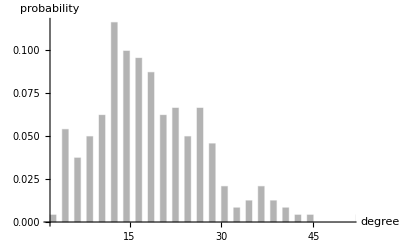

### Global Clustering Coefficient

```mathematica
GlobalClusteringCoefficient[graph];
```

1008/4013

## Graph Communities

### Communities Count

```mathematica
Length[FindGraphCommunities[graph]];
```

5

### Communities Plot

```mathematica
CommunityGraphPlot[graph];
```

-Graphics-

## Graph Spectra

### Graph Spectra

```mathematica
A = AdjacencyMatrix[graph];
{eigenVals,eigenVecs} =Eigensystem[N[A]];
laplacian = KirchhoffMatrix[graph];
{minEigenVal, minEigenVec} = Eigensystem[N[A], -1];
```

## Node Centralities

### PageRank Centrality

```mathematica
MaxPageRankCentralNode = VertexList[graph][[Position[PageRankCentrality[graph], 
Max[PageRankCentrality[graph]]][[1]]]];
HighlightGraph[graph, MaxPageRankCentralNode];
```

{127}

-Graphics-

### Degree Centrality

```mathematica
MaxDegreeCentralNode = VertexList[graph][[Position[DegreeCentrality[graph], 
Max[DegreeCentrality[graph]]][[1]]]];
HighlightGraph[graph, MaxDegreeCentralNode];
```

{127}

-Graphics-

### Closeness Centrality

```mathematica
MaxClosenessCentralityNode = VertexList[graph][[Position[ClosenessCentrality[graph], 
Max[ClosenessCentrality[graph]]][[1]]]];
HighlightGraph[graph, MaxClosenessCentralityNode];
```

{127}

-Graphics-

### Betweenness Centrality

```mathematica
MaxBetweenessCentralityNode = VertexList[graph][[Position[BetweennessCentrality[graph], 
Max[BetweennessCentrality[graph]]][[1]]]];
HighlightGraph[graph, MaxBetweenessCentralityNode];
```

{15}

-Graphics-

### EigenVector Centrality

```mathematica
MaxEigenVectorCentralityNode = VertexList[graph][[Position[EigenvectorCentrality[graph], 
Max[EigenvectorCentrality[graph]]][[1]]]];
HighlightGraph[graph, MaxEigenVectorCentralityNode];
```

{15}

-Graphics-

### Clustering Coefficient

```mathematica
MaxClusterNode = VertexList[graph][[Position[LocalClusteringCoefficient[graph], 
Max[LocalClusteringCoefficient[graph]]][[1]]]];
HighlightGraph[graph, MaxClusterNode];
```

{95}

-Graphics-